# Numeric QM (Schiff “Quantum Mechanics”, chapter 6)

### Parametry symulacji

```mathematica
nmax=100; (* wymiar przestrzeni stanów *)
k=Ceiling[nmax/4]; (* numer funkcji falowej *)
```

### Operatory anihilacji i kreacji

```mathematica
$PrePrint=MatrixForm; (* wyświetlanie w formie macierzowej *)
a=Table[Which[n==m-1,√n,True,0],{n,nmax},{m,nmax}]; (* operator anihilacji *)
adag=Transpose[a]; (* operator kreacji *)
a.adag-adag.a; (* sprawdzenie komutatora [a,a^+]=1 *)
```

### Hamiltonian oscylatora harmonicznego

```mathematica
h=1/2 IdentityMatrix[nmax]+adag.a;
```

### Operatory położenia i pędu

```mathematica
x=1/√2(adag+a); (* operator położenia *)
p=I/√2(adag-a); (* operator pędu *)
x.p-p.x; (* sprawdzenie komutatora [x,p]=ⅈ *)
```

### Zagadnienie własne dla oscylatora harmonicznego

```mathematica
Sort[Eigenvalues[N[x]]]; (* wartości własne operatora położenia *)
Sort[Eigenvalues[N[p]]]; (* wartości własne operatora pędu *)
wyn1h=Sort[Eigenvalues[N[h]]]; (* wartości własne Hamiltonianu oscylatora *)
wyn=Eigensystem[N[x]]; (* wartości i wektory własne operatora położenia *)
```

### Funkcje falowe oscylatora w reprezentacji położeniowej (brak normalizacji)

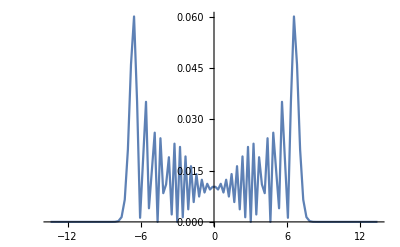

```mathematica
xn1=Sort[Table[{wyn[[1]][[n]],n},{n,nmax}]]; (* sortowanie wartości własnych *)
xn2=Transpose[Table[wyn[[2,xn1[[n,2]]]],{n,nmax}]]; (* sortowanie wektorów własnych *)
pom=Table[{Sort[wyn[[1]]][[j]],(Abs[xn2[[k]]]^2)[[j]]},{j,nmax}]; (* lista par {x,Subscript[ψ, k](x)} *)
r1=ListPlot[pom,Joined->True,PlotRange->All] (* wyświetlanie wybranych fukcji falowych w reprezentacji położeniowej *)
```

### Hamiltonian z potencjałem V(x) = x^4

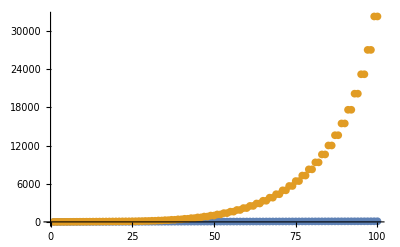

```mathematica
h2=1/2 p.p+(x.x).(x.x);
wyn2h=Sort[Eigenvalues[N[h2]]]; (* wartości własne Hamiltonianu z potencjałem V(x)=x^4 *)
ListPlot[{wyn1h,wyn2h},PlotRange->All](* porównanie widma z hamiltonianem oscylatora harmonicznego *)
```

### Funkcje falowe hamiltonianu V(x) = x^4 (brak normalizacji)

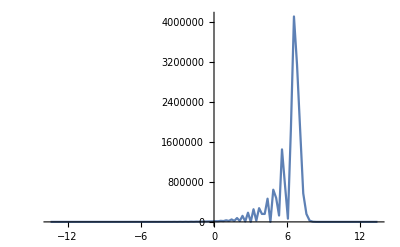

```mathematica
xn3=Table[wyn[[2,xn1[[n,2]]]],{n,nmax}]; (* sortowanie wektorów własnych *)
pom2=Table[{Sort[wyn[[1]]][[j]],(Abs[Transpose[(wyn2h xn3)][[k]]]^2)[[j]]},{j,nmax}]; (* lista sumowanych par {x,Subscript[ψ, k](x)} *)
r2=ListPlot[pom2,Joined->True,PlotRange->All] (* wyświetlanie wybranych fukcji falowych w reprezentacji położeniowej *)
```

### Porównanie funkcji falowych obu hamiltonianów (brak normalizacji)

```mathematica
Manipulate[xn1=Sort[Table[{wyn[[1]][[n]],n},{n,nmax}]]; (* sortowanie wartości własnych *)
xn2=Transpose[Table[wyn[[2,xn1[[n,2]]]],{n,nmax}]]; (* sortowanie wektorów własnych *)
pom=Table[{Sort[wyn[[1]]][[j]],(Abs[xn2[[k]]]^2)[[j]]},{j,nmax}]; (* lista par {x,Subscript[ψ, k](x)} *)
r1=ListPlot[pom,Joined->True,PlotRange->All];
xn3=Table[wyn[[2,xn1[[n,2]]]],{n,nmax}]; (* sortowanie wektorów własnych *)
pom2=Table[{Sort[wyn[[1]]][[j]],(Abs[Transpose[(wyn2h xn3)][[k]]]^2)[[j]]},{j,nmax}]; (* lista sumowanych par {x,Subscript[ψ, k](x)} *)
r2=ListPlot[pom2,Joined->True,PlotRange->All];GraphicsGrid[{{r1,r2}},ImageSize->900],{{k,Ceiling[nmax/8]},1,nmax,1}] (* wyświetlanie kolejnych fukcji falowych w reprezentacji położeniowej *)
```

### (* analogicznie dla innych potencjałów → np. potencjału Higgs'a V(x)=x^4-x^2 *)